

```mathematica
sinPlot=Plot[Sin[x],{x,0,2Pi}]
```

```mathematica
Short[InputForm[sinPlot],14]
```

Graphics[{{{{}, {}, Annotation[{Directive[Opacity[1.], RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], Line[{{1.2822827157509358*^-7, 1.2822827157509324*^-7}, {0.0019271655319089223, 0.001927164339004283}, {0.0038542028355462695, 0.00385419329326691}, {0.007708277442820964, 0.007708201108565738}, {0.015416426657370353, 0.015415816004008815}, {0.030832725086469132, 0.030827840094677948}, {0.06166532194466669, 0.061626247826437476}, {0.1233305156610618, 0.12301810194283724}, {0.2570347881802097, 0.2542138749185557}, {0.3818787050494512, 0.3726645007390021}, {0.504273679847541, 0.4831716559080398}, {0.6370425397319885, <<1>>}, <<413>>, {6.2702463305911404, -0.012938615557112596}, {6.274559280044532, -0.008625920160720309}, {6.276715754771227, -0.006469507277817619}, {6.278872229497923, -0.004313064309238329}, {6.281028704224619, -0.0021566012832639164}, {6.283185178951315, -1.28228271801381*^-7}}]}, <<1>>]}}, {}}, {<<25>>}]

```mathematica
z=8+3I;
```

```mathematica
line1=Line[{{0,0},{Re[z],Im[z]}}];
```

```mathematica
point1={PointSize[.02],Point[{Re[z],Im[z]}]};
```

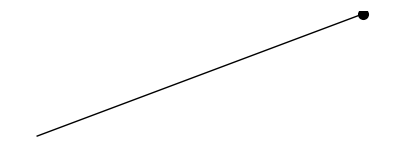

```mathematica
Show[Graphics[{line1,point1}]]
```

```mathematica
cz=Conjugate[z];
line2=Line[{{0,0},{Re[cz],Im[cz]}}];
point2={PointSize[.02],Point[{Re[cz],Im[cz]}]};
```

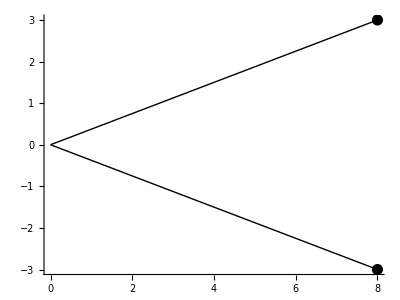

```mathematica
Show[Graphics[{line1,point1,line2,point2},Axes->True]]
```

```mathematica
hline={Dashing[{0.04,0.04}],Line[{{0,Im[z]},{Re[z],Im[z]}}]};
```

```mathematica
vline={Dashing[{0.04,0.04}],Line[{{Re[z],0},{Re[z],Im[z]}}]};
```

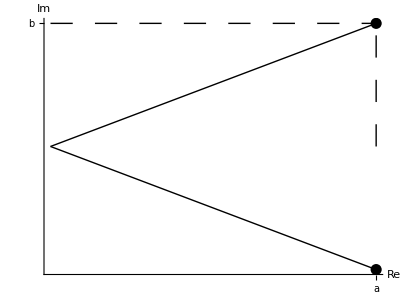

```mathematica
Show[Graphics[{line1,point1,line2,point2,hline,vline},
Axes->True,AxesLabel->{Re,Im},
Ticks->{{{Re[z],"a"}},{{Im[z],"b"}}},
AspectRatio->Automatic]]
```

```mathematica
Text["z=a+bi",{Re[z]-.75,Im[z]+.35}]
```

Text[z=a+bi,{7.25,3.35}]

```mathematica
Text[FontForm["z=a+bi",{"Times-Italic",9}],
{Re[z]-.75,Im[z]+.35}];
```

```mathematica
text1=Text[FontForm["z=a+bi",
{"Times-Italic",10}],
{Re[z]-.75,Im[z]+.35}];
```

```mathematica
text2=Text[FontForm["Abs[z]",{"Times-Italic",10}],
{3.5,2}];
```

```mathematica
text3=Text[FontForm["Conjugate[z]=a-bi",
{"Times-Italic",10}],
{Re[cz]-1.4,Im[cz]-.35}];
```

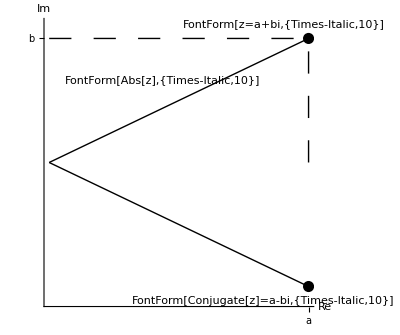

```mathematica
Show[Graphics[{line1,line2,point1,point2,
hline,vline,text1,text2,text3},
Axes->True,
AxesLabel->{Re,Im},
Ticks->{{{Re[z],"a"}},{{Im[z],"b"}}},
AspectRatio->Automatic]]
```

```mathematica
arc=Circle[{0,0},Abs[z]/3,{0,Arg[z]}];
```

```mathematica
text4=Text[FontForm["Arg[z]",{"Times-Italic",10}],
{3.5,.5}];
```

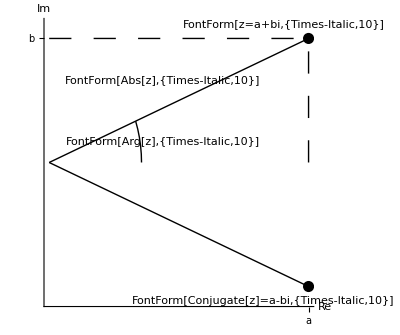

```mathematica
Show[Graphics[
{line1,line2,point1,point2,hline,vline,
text1,text2,text3,text4,arc},
Axes->True,AxesLabel->{Re,Im},
Ticks->{{{Re[z],"a"}},{{Im[z],"b"}}},
AspectRatio->Automatic]]
```

```mathematica
Map[{Cos[#],Sin[#],#/N[Pi]-1}&,
{Random[Real,{0,N[2Pi]}]}]
```

{{0.903486,-0.428619,0.859}}

```mathematica
randomWalk3D[n_Integer]:=
FoldList[Plus,{0,0,0},
Map[{Cos[#],Sin[#],#/N[Pi]-1}&,
Table[Random[Real,{0,N[2Pi]}],{n}]]]
```

```mathematica
showRandomWalk3D[n_Integer]:=
Show[Graphics3D[Line[randomWalk3D[n]]]]
```

```mathematica
showRandomWalk3D[1000]
```

-Graphics3D-

```mathematica
coords[n_]:=Table[Random[],{n},{2}]
```

```mathematica
Show[Graphics[Map[Point,coords[10]]]]
```

-Graphics-

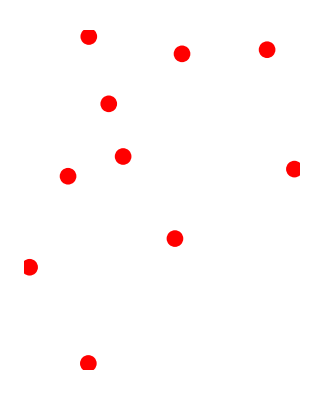

```mathematica
Show[Graphics[
{RGBColor[1,0,0],PointSize[.03],
Map[Point,coords[10]]}]]
```

```mathematica
c=Circle[{0,0},1];
```

```mathematica
ctext=Text[FontForm["Circle",{"Times-Italic",12}],
{Cos[5Pi/4]+.25,Sin[5Pi/4]}];
```

```mathematica
t=Line[{{-1,0},{0,1},{1,0},{-1,0}}];
```

```mathematica
ttext=Text[FontForm["Triangle",{"Times-Italic",12}],
{0,0+.05}];
```

```mathematica
r=Line[{{-1,-1},{-1,1},{2,1},{2,-1},{-1,-1}}];
```

```mathematica
rtext=Text[FontForm["Rectangle",{"Times-Italic",12}],
{1.5,-1+.05}];
```

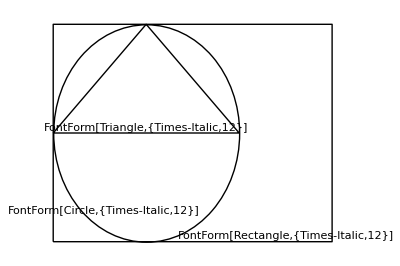

```mathematica
Show[Graphics[{c,t,r,ctext,ttext,rtext}],
AspectRatio->Automatic]
```

```mathematica
Map[Cuboid[#]&,Table[Random[],{2},{3}]]
```

{Cuboid[{0.140813,0.953641,0.920411}],Cuboid[{0.36079,0.106682,0.640927}]}

```mathematica
cubes=Map[Cuboid[#]&,Table[Random[],{6},{3}]];
```

```mathematica
Show[Graphics3D[cubes]]
```

-Graphics3D-

```mathematica
randomWalk3D[n_Integer]:=
Module[{m=Random[Integer,{1,5}]},
FoldList[Plus,{0,0,0},
Map[{Cos[#]/m,Sin[#]/m,Sqrt[m^2-1]/m}&,
Table[Random[Real,{0,N[2Pi]}],{n}]]
]]
```

```mathematica
r3=randomWalk3D[2]
```

{{0,0,0},{-0.193101,-0.158782,(√15)/4},{-0.034331,-0.351894,(√15)/2}}

```mathematica
distance[{a_},{b_}]:=
Sqrt[Apply[Plus,(b-a)^2]]
```

```mathematica
distance[{r3[[2]],r3[[3]]}]
```

distance[{{-0.193101,-0.158782,(√15)/4},{-0.034331,-0.351894,(√15)/2}}]

```mathematica
Needs["Graphics`Polyhedra`"]
```

Get::noopen: Cannot open Graphics`Polyhedra`.

Needs::nocont: Context Graphics`Polyhedra` was not created when Needs was evaluated.

$Failed

```mathematica
Needs["Graphics`Polyhedra`*"]
```

Needs::cxt: Invalid context specified at position 1 in Needs[Graphics`Polyhedra`*]. A context must consist of valid symbol names separated by and ending with `.

Needs[Graphics`Polyhedra`*]

```mathematica
solids=Map[Graphics3D,
{Cube[],Dodecahedron[],GreatDodecahedron[],
GreatIcosahedron[],GreatStellatedDodecahedron[],
Icosahedron[],Octahedron[],Tetrahedron[],
SmallStellatedDodecahedron[]}];
```

```mathematica
gr={Map[solids[[#]]&,Range[5]],
Map[solids[[#]],Range[6,9]]}
```

Part::pkspec1: The expression #1 cannot be used as a part specification.

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}⟦#1⟧[6],{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}⟦#1⟧[7],{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}⟦#1⟧[8],{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}⟦#1⟧[9]}}

```mathematica
Show[GraphicsArray[gr]]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

Part::pkspec1: The expression {Center,Center} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-Graphics-